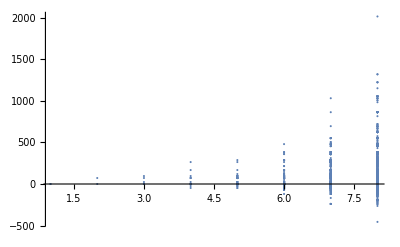

```mathematica
ListPlot[
Flatten[
Table[
With[
{k=mpgBounds[[m]]},
Table[{m,dops2[[i,2]]-dops2[[i,1]]},{i,k[[1]],k[[2]]}]
]
,{m,1,8}]
,1], PlotRange->All]
```

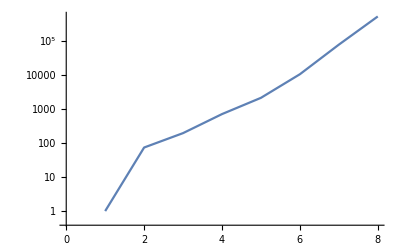

```mathematica
ListLogPlot[{0,72,192,696,2088,10272,75600,507312}+1, Joined->True]
```

```mathematica
TableForm[
Table[
Map[Flatten[#]&,Tally[Sort[Select[Table[dops2[[i]],{i,k[[1]],k[[2]]}],#[[1]]>#[[2]]&]]]]
,{k,Most[mpgBounds]}],
TableDepth->1
]
```

```mathematica
Take[
Table[
Sort[Map[{#[[2]],#[[1,3]]}&,
Select[
Table[{dops2[[i]],i},{i,k[[1]],k[[2]]}],
{#[[1,1]],#[[1,2]]}=={24,96}&
]
]
]
,{k,Most[mpgBounds]}],
5
]
```

{{},{{4,{2,3<->4}}},{{7,{2,2<->5}}},{{16,{2,3<->6}},{17,{2,4<->6}}},{{26,{2,3<->6}},{31,{2,2<->7}},{47,{2,2<->5}},{52,{2,2<->7}},{70,{2,2<->7}},{71,{2,2<->5}}}}

```mathematica
Table[Map[{#[[1]],#[[2]]}&,k],{k,{{{4,"{2,3<->4}"}},{{7,"{2,2<->5}"}},{{16,"{2,3<->6}"},{17,"{2,4<->6}"}},{{26,"{2,3<->6}"},{31,"{2,2<->7}"},{47,"{2,2<->5}"},{52,"{2,2<->7}"},{70,"{2,2<->7}"},{71,"{2,2<->5}"}}}}]
```

{{{4,{2,3<->4}}},{{7,{2,2<->5}}},{{16,{2,3<->6}},{17,{2,4<->6}}},{{26,{2,3<->6}},{31,{2,2<->7}},{47,{2,2<->5}},{52,{2,2<->7}},{70,{2,2<->7}},{71,{2,2<->5}}}}

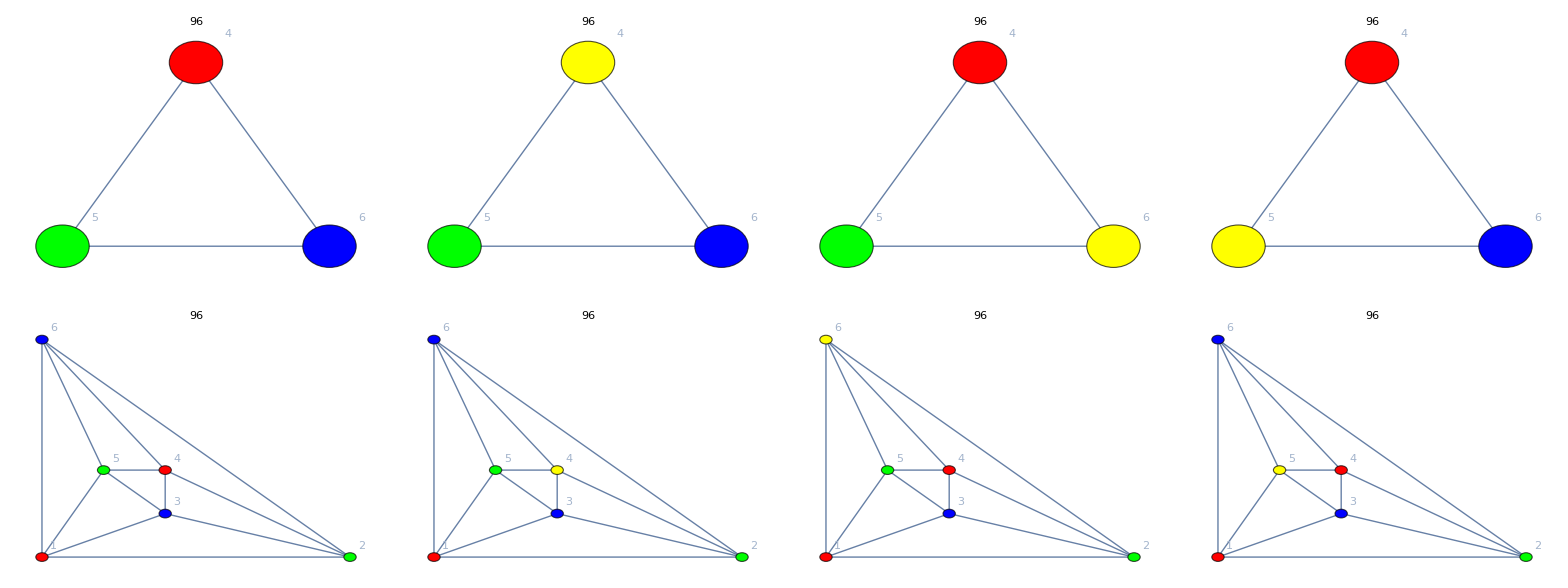
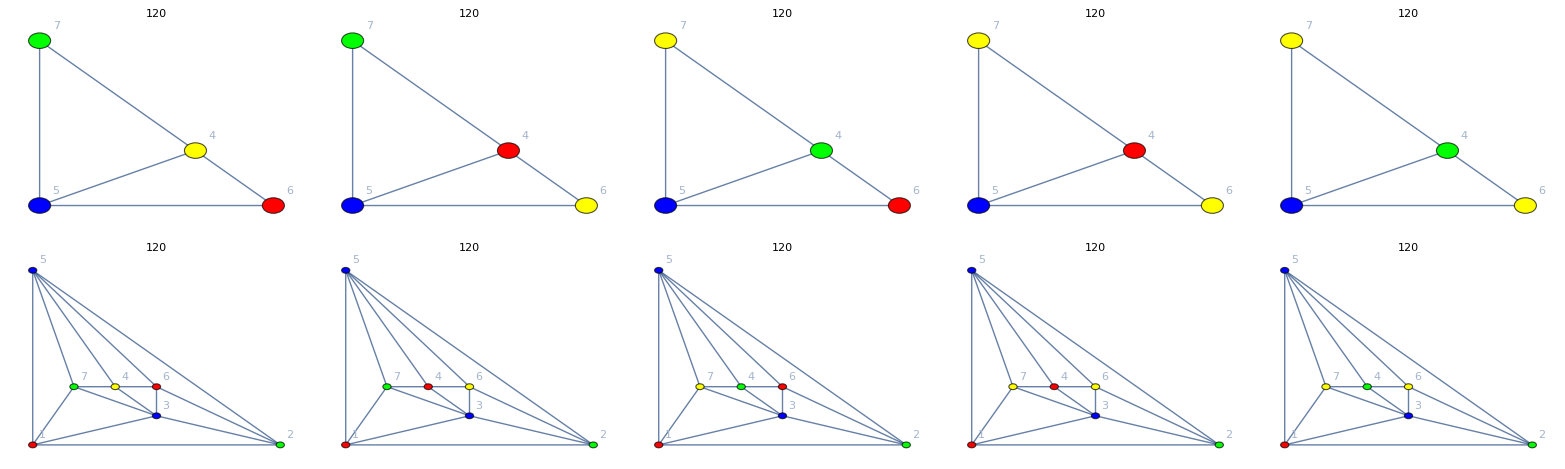
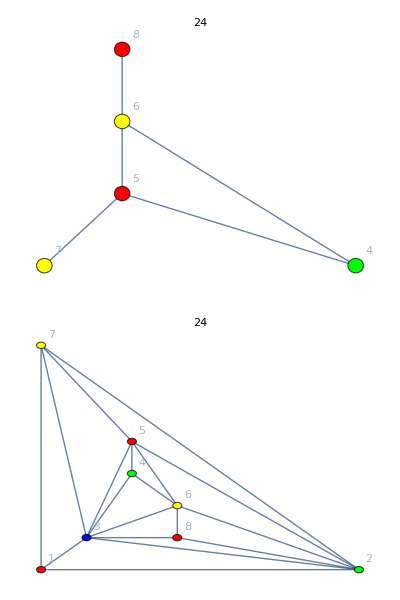
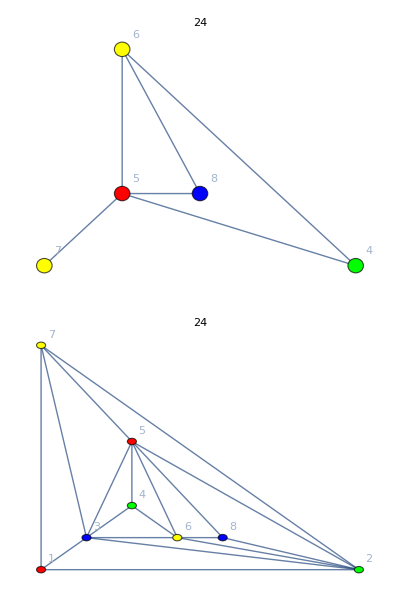
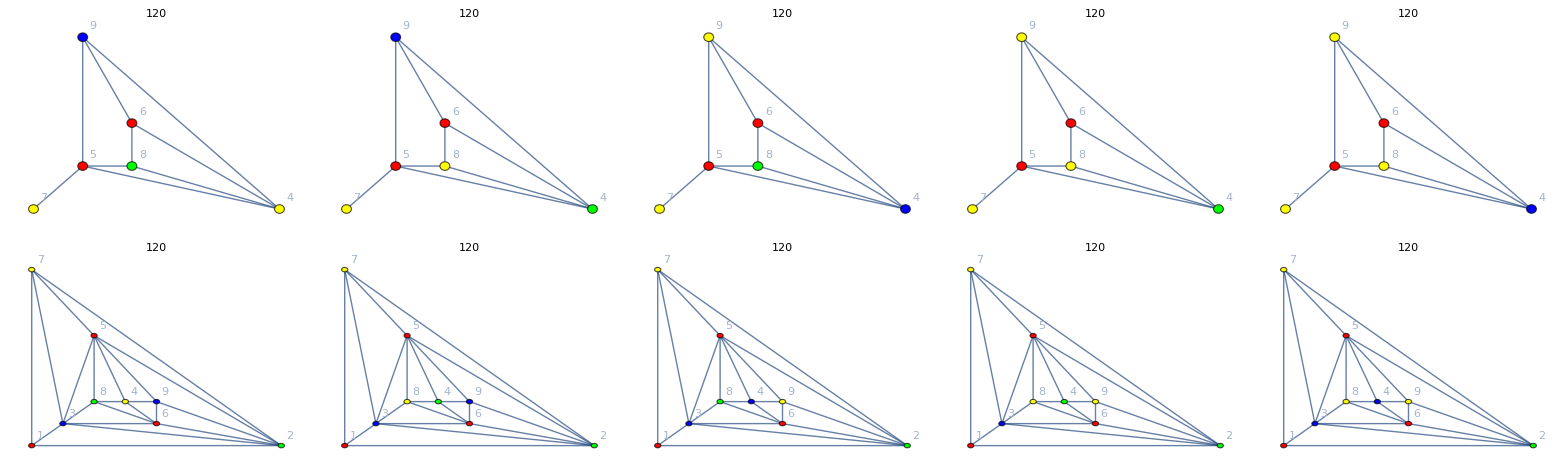
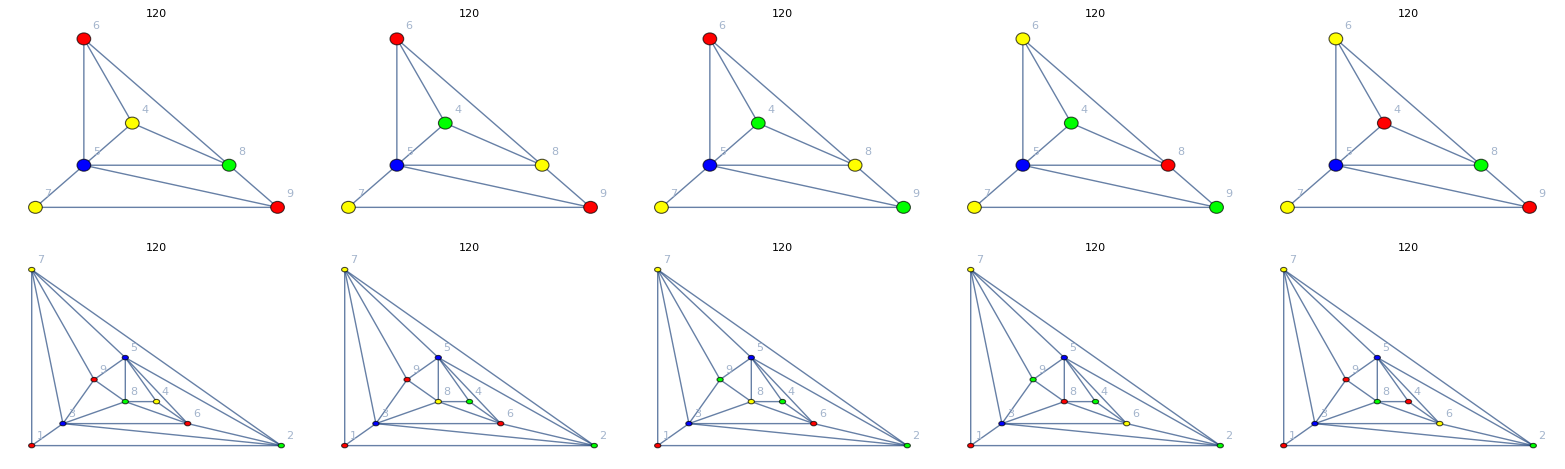
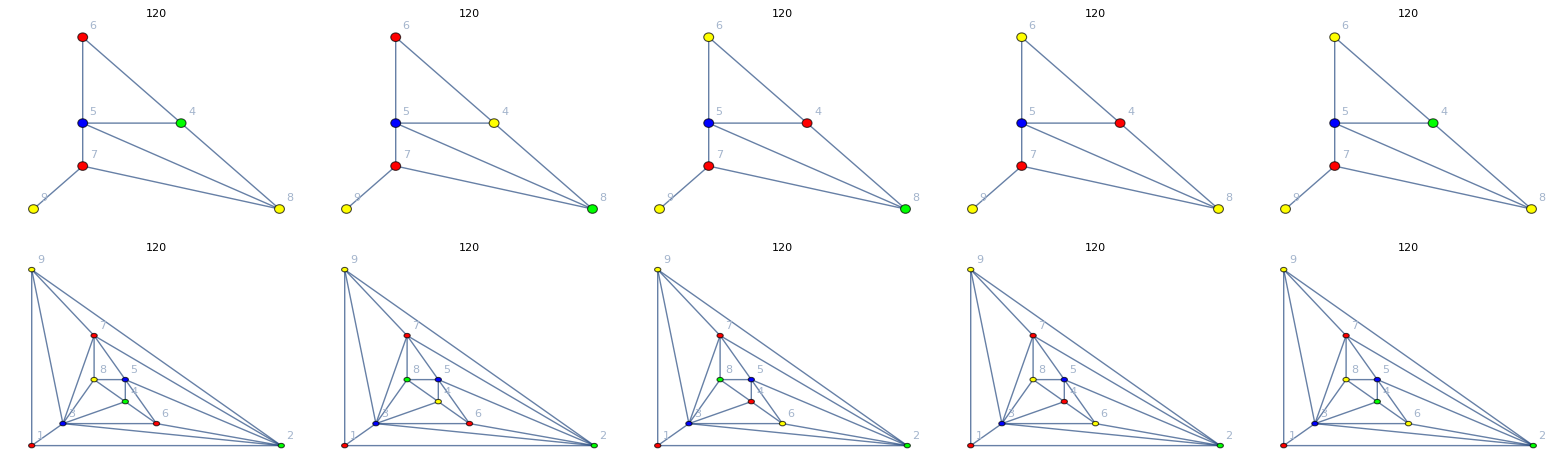
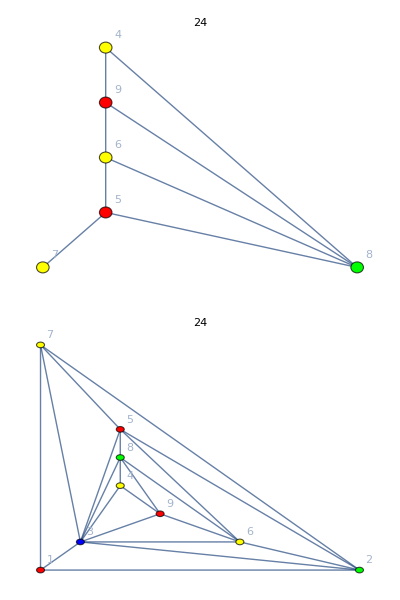
-Graphics- |  |  |  |  | 
-Graphics- |  |  |  |  | 
-Graphics- | -Graphics- |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[Map[PaintGraph[Graph[ReadGrof[#[[1]]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name", PlotLabel->#[[2]]]]&,k],{k,{{{4,"{2,3<->4}"}},{{7,"{2,2<->5}"}},{{16,"{2,3<->6}"},{17,"{2,4<->6}"}},{{26,"{2,3<->6}"},{31,"{2,2<->7}"},{47,"{2,2<->5}"},{52,"{2,2<->7}"},{70,"{2,2<->7}"},{71,"{2,2<->5}"}}}}]]
```

```mathematica
{{},{3},{5},{13,14,21},{24,26,30,35,53,55,60,63,64,65}}
Map[Map[ReadGrof[#]&,#]&,{{3},{5},{13,14,21},{24,26,30,35,53,55,60,63,64,65}}]
```

{{},{3},{5},{13,14,21},{24,26,30,35,53,55,60,63,64,65}}

OpenRead::noopen: Cannot open "D:\\Grofs\\{3}.grof".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

$Aborted

```mathematica
TableForm[
Table[
Map[Flatten[#]&,Tally[Sort[Select[Table[dops3[[i]],{i,k[[1]],k[[2]]}],#[[1]]>#[[2]]&]]]]
,{k,Most[mpgBounds]}],
TableDepth->1
]
```

{}
{}
{}
{{96,72,1}}
{{96,72,1},{120,48,1},{120,72,3}}
{{72,48,1},{96,48,3},{96,72,18},{120,48,3},{120,72,12},{288,144,1}}
{{72,48,9},{96,48,4},{96,72,69},{120,48,11},{120,72,45},{144,120,1},{216,120,1},{216,144,1},{216,168,1},{288,120,3},{288,144,8},{288,168,2},{288,216,5},{288,264,2},{384,312,1},{504,168,1}}
{{72,48,111},{96,48,27},{96,72,295},{120,48,61},{120,72,256},{120,96,2},{144,96,4},{144,120,22},{168,96,1},{168,144,1},{192,168,1},{216,96,5},{216,120,40},{216,144,30},{216,168,43},{216,192,3},{264,96,7},{264,144,7},{264,168,1},{264,240,2},{288,96,1},{288,120,17},{288,144,52},{288,168,25},{288,192,3},{288,216,26},{288,264,15},{312,192,1},{312,216,1},{312,240,1},{312,264,2},{336,168,1},{336,192,1},{336,216,2},{336,240,3},{336,264,2},{336,312,2},{384,192,1},{384,216,5},{384,264,8},{384,288,26},{384,312,24},{384,336,3},{480,168,1},{480,192,1},{480,216,3},{480,264,4},{480,288,13},{480,312,6},{480,360,3},{480,384,2},{504,144,1},{504,168,6},{504,264,1},{504,336,1},{672,384,1},{672,528,1},{1056,336,1}}

```mathematica
ListPlot3D[
Map[{Log[#[[1]]],Log[#[[2]]],#[[3]]}&,
Flatten[
Table[
Map[Flatten[#]&,Tally[Sort[Table[dops2[[i]],{i,k[[1]],k[[2]]}]]]]
,{k,Most[mpgBounds]}],1
]
]
]
```

-Graphics3D-

```mathematica
Table[
With[
{k=mpgBounds[[m]]},
Max[Table[dops2[[i,2]]/24,{i,k[[1]],k[[2]]}]]
]
,{m,1,8}]
```

{1,4,5,12,16,21,44,85}

```mathematica
Jacobsthal
```

{0,2,1,4,5,12,21,44,85,172,341,684,1365,2732,5461}